Mats-Erik Pistol

Solid State Physics and NanoLund, 
Lund University, Lund, Sweden

## This section contains the code to construct isospectral sets.

The commands in the following cell are as follows: 
ConnectedGraphs[n] loads all connected graphs with n vertices. n should be at most 7. If n is larger than 7, not all graphs are loaded since they are lacking in Wolframs database. 
ConnectedGraphsAll[n] loads all connected graphs with 2 to n vertices. n should be at most 7 to get all graphs. 
I think ConnectedGraphs[2;;n] loads all loads all connected graphs with at most n vertices, excluding the single vertex graph. 
PendantEdgeAdd[h, n] gives all the graphs obtained from h, where exactly n pendant edges have been added. The default value of n is one.
PendantEdgeAddAll[h,n] gives all the graphs obtained from h, where between 0 and n pendant edges have been added, 0 and n inclusive.
IsospectralPairs[h] returns all tentative isospectral pairs from the list h.
IsospectralPairsFromData[h, tab] returns all tentative isospectral pairs from the list h, but using a precomputed list of roots: tab, probably read from disk.
EulerCharacteristicGraph[h] returns the Euler characteristic for the graph h.
DeterminantD[h] gives the secular determinant, D(k), for the graph h. DeterminantD[mo] is defined in GraphRoots and is used to check multiplicities.
Allconnected⟦i⟧ gives graph i from all connected graphs having at most 7 vertices.
GraphAddContract[u, v, a, b]  Here we attach u to v and identify vertices a and b, where a belongs to u and b belongs to v. 
GraphAddContract2[u, v1, v2, u1a, u2a, v1a, v2a]   Here we attach v1 and v2 to u and identify vertices u1a with v1a and u2a with v2a. 
GraphAddContract3[u, v1, v2, v3, u1a, u2a, u3a, v1a, v2a, v3a]   Here we attach v1, v2 and v3 to u and identify vertices u1a with v1a, u2a with v2a and u3a with v3a.
GraphAddContract4[u, v1, v2, v3, v4, u1a, u2a, u3a, u4a, v1a, v2a, v3a, v4a]  Here we attach v1, v2, v3 and v4 to u and identify vertices u1a with v1a, u2a with v2a, u3a with v3a and u4a with v4a.

```mathematica
ConnectedGraphs[n_]:=Module[{graphs},graphs=GraphData/@GraphData[n];
   Cases[graphs,x_/; Length@WeaklyConnectedComponents[x]==1]]

ConnectedGraphsAll[n_]:=Module[{graphs},graphs=GraphData/@GraphData[2;;n];
   Cases[graphs,x_/; Length@WeaklyConnectedComponents[x]==1]]

PEA[h_]:=
Module[{tmp},tmp=Table[EdgeAdd[h,i<->VertexCount[h]+1],{i,1,VertexCount[h]}]//Flatten;
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp]]

PendantEdgeAdd[h_,n_:1]:=Module[{tmp},tmp=Nest[Flatten@(PEA/@#1)&,{h},n];
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp]];

PendantEdgeAdd::usage=
"PendantEdgeAdd[h, n] gives all the graphs obtained from h, where exactly n pendant edges have been added. The default value of n is one.";

PendantEdgeAddAll[h_,n_]:=Module[{tmp},tmp=Flatten@Table[Nest[Flatten@(PEA/@#1)&,{h},i],{i,1,n}];
tmp=DeleteDuplicates[tmp,IsomorphicGraphQ[#1,#2]&];
Return[tmp∪{h}]];

PendantEdgeAdd::usage=
"PendantEdgeAddAll[h,n] gives all the graphs obtained from h, where between 0 and n pendant edges have been added.";

IsospectralPairs[h_List]:=Module[{tab,aaa,int,grapp,grappduplicatefree},
tab=Table[NGraphRoots[h⟦i⟧,5]/π,{i,1,Length[h]}]; (* Here we generate a table of the numerical eigenvalues *)

aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs]];

IsospectralPartners[g_,h_List]:=Module[{tab,target,int,grapp,grappduplicatefree},
tab=Table[NGraphRoots[h⟦i⟧,5]/π,{i,1,Length[h]}]; (* Here we generate a table of the numerical eigenvalues *)
target=NGraphRoots[g,5]/π;
int=Position[tab,target];  
grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;
Return[grappduplicatefree]];

IsospectralPairsFromData[h_List,tab_]:=
Module[{aaa},aaa=Values@PositionIndex[tab];  (* PositionIndex gives an association between the unique values in tab and their position. Note unique. *)
int=Select[aaa,Length[#]>1&]; (* Here we select those values that are not unique. *)   

grapp=Table[h⟦int⟦i⟧⟧,{i,1,Length[int]}];
grappduplicatefree=DeleteDuplicates[#,IsomorphicGraphQ[#1,#2]&]&/@grapp;

isopairs=Select[grappduplicatefree, Length[#]>1&];
Return[isopairs];];

EulerCharacteristicGraph[h_Graph]:=VertexCount@h-EdgeCount@h;

GraphAddContract[u_,v_,a_,b_]:=VertexContract[#,{a,b}]&@Graph[EdgeList[u]∪EdgeList[v]∪{a<->b}]; (* Here we attach u to v and identify vertices a and b *)
GraphAddContract::usage=
"GraphAddContract[u,v,a,b] attaches u to v identifying vertices a of u to b of v.";

GraphAddContract2[u_,v1_,v2_,u1a_,u2a_,v1a_,v2a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪{u1a<->v1a,u2a<->v2a}];
(* Here we attach v1 and v2 to u and identify vertices u1a with v1a and u2a with v2a *)
GraphAddContract2::usage=
"GraphAddContract2[u,v1,v2,u1a,u2a,v1a,v2a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a.";

GraphAddContract3[u_,v1_,v2_,v3_,u1a_,u2a_,u3a_,v1a_,v2a_,v3a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a},{u3a,v3a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪EdgeList[v3]∪{u1a<->v1a,u2a<->v2a,u3a<->v3a}];
(* Here we attach v1, v2 and v3 to u and identify vertices u1a with v1a, u2a with v2a and u3a with v3a *)
GraphAddContract3::usage=
"GraphAddContract2[u,v1,v2,v3,u1a,u2a,u3a,v1a,v2a,v3a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a and u3a with v3a.";

GraphAddContract4[u_,v1_,v2_,v3_,v4_,u1a_,u2a_,u3a_,u4a_,v1a_,v2a_,v3a_,v4a_]:=VertexContract[#,{{u1a,v1a},{u2a,v2a},{u3a,v3a},{u4a,v4a}}]&@Graph[EdgeList[u]∪EdgeList[v1]∪EdgeList[v2]∪EdgeList[v3]∪EdgeList[v4]∪{u1a<->v1a,u2a<->v2a,u3a<->v3a,u4a<->v4a}];
(* Here we attach v1, v2, v3 and v4 to u and identify vertices u1a with v1a, u2a with v2a, u3a with v3a and u4a with v4a *)
GraphAddContract4::usage=
"GraphAddContract2[u,v1,v2,u1a,u2a,u3a,u4a,v1a,v2a,v3a,v4a] attaches u to v1 and v2 identifying vertices u1a of u to v1a of v1 and u2a with v2a and u3a with v3a and u4a with v4a.";


 Allconnected=ConnectedGraphsAll[7]; (* Here we get some graphs from Wolframs database. *)
h=.;
atable=Table[i->Subscript[a, i],{i,55}];
btable=Table[i->Subscript[b, i],{i,55}];
ctable=Table[i->Subscript[c, i],{i,55}];
dtable=Table[i->Subscript[d, i],{i,55}];(* Useful tables *)
etable=Table[i->Subscript[e, i],{i,55}];
ftable=Table[i->Subscript[f, i],{i,55}];
gtable=Table[i->Subscript[g, i],{i,55}]; 
htable=Table[i->Subscript[h, i],{i,55}]; 
ktable=Table[i->Subscript[k, i],{i,55}]; 

utable=Table[i->Subscript[u, i],{i,55}];
vtable=Table[i->Subscript[v, i],{i,55}];
wtable=Table[i->Subscript[w, i],{i,55}];
```

## The following section constructs the isospectral pairs in the paper.

First we do it for all connected graphs with at most seven vertices.

```mathematica
isospectralpairsconnected=IsospectralPairs[Allconnected]; (* Here we find suspect isospectral pairs. They have to be checked for multiplicity of their roots. *)
```

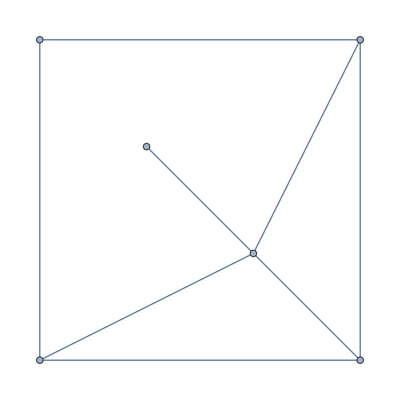
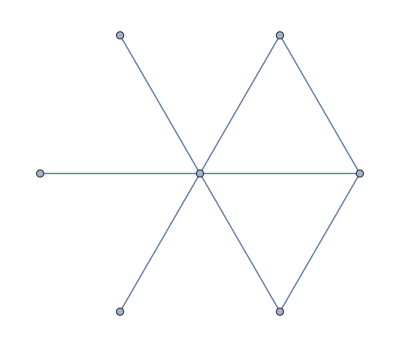
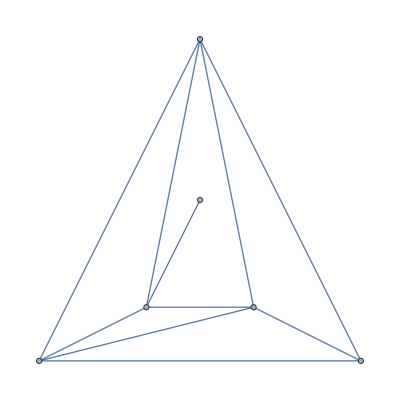
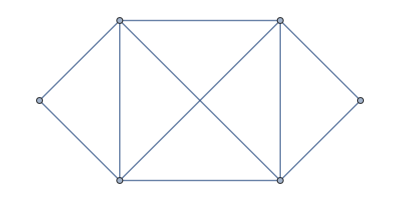
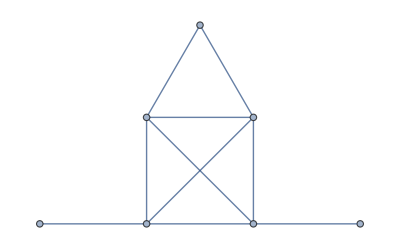
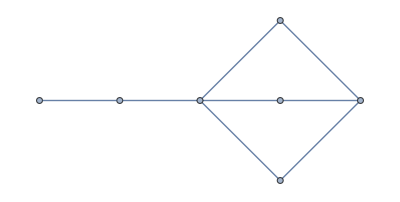
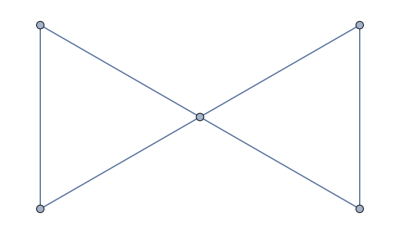
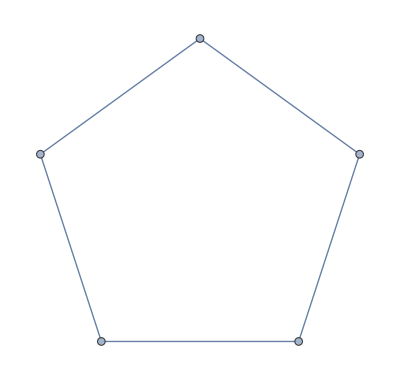
Small[{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}]

```mathematica
isospectralpairsconnected//Small (* These are the suspects. Many can immediately be eliminated after checking Euler characteristics or for reasons such as being clearly isomorphic. *)
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-,-Graphics-}//FullSimplify (* We here check for multiplicity. Each pair or set is checked individually. *)
```

{-576 ⅈ Sin[k/3]^3,6144 Sin[k/6]^2 Sin[k/3]^2,384 ⅈ Cos[k/6]^5 Sin[k/6]}

```mathematica
Finalisospectralpairsconnected={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}; (* These are the final isospectral pairs with at most seven vertices after checking multiplicities. *)
```

```mathematica
Map[GraphPlot[EdgeList@#,GraphLayout->"SpringElectricalEmbedding",ImageSize->70]&]/@Finalisospectralpairsconnected
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}
```

{-192 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/2))^3 (1+ⅇ^((ⅈ k)/2)),-64 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/2))^3 (1+ⅇ^((ⅈ k)/2))}

Then for trees with at most ten vertices

```mathematica
trees=PendantEdgeAddAll[-Graphics-,8];
```

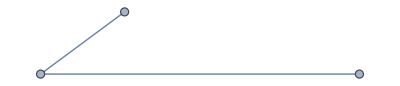
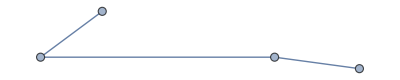
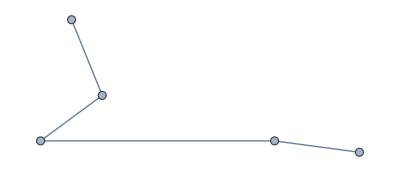
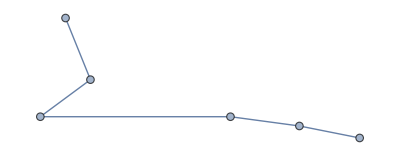
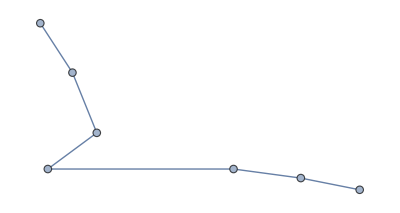
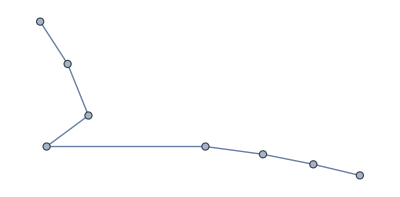
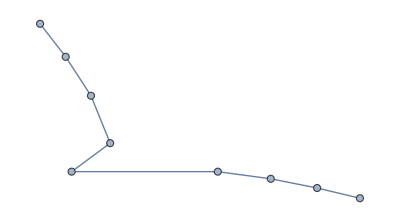
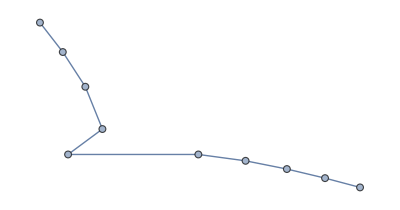
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
suspecttrees=IsospectralPairs[trees]
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify//Factor  (* We here check for multiplicity. Each pair is checked individually. *)
```

{-48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^2 (1-ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((4 ⅈ k)/9)) (3-4 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((4 ⅈ k)/9)),48 ⅇ^(-ⅈ k) (-1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)) (1+ⅇ^((2 ⅈ k)/9))^2 (1-ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((ⅈ k)/9)+ⅇ^((2 ⅈ k)/9)) (1+ⅇ^((4 ⅈ k)/9)) (3-4 ⅇ^((2 ⅈ k)/9)+3 ⅇ^((4 ⅈ k)/9))}

```mathematica
Finalisospectraltrees={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}};
(* The final checked trees with at most ten vertices *)
Map[GraphPlot[EdgeList@#,GraphLayout->"SpringEmbedding",ImageSize->70]&]/@Finalisospectraltrees
```

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} (* Different embedding. *)
```

Here we do it for trees with twelve vertices.

```mathematica
treesten=PendantEdgeAddAll[-Graphics-,10]; (* Lets do it with up to 12 vertices. This takes a few hours on a laptop. *)
```

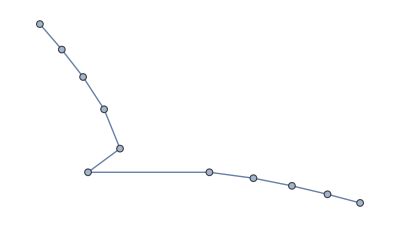
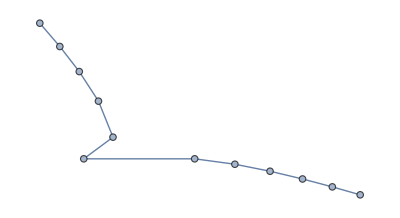
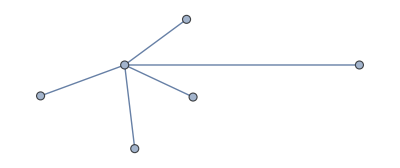
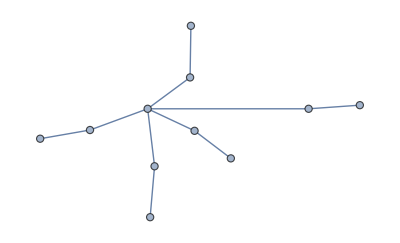
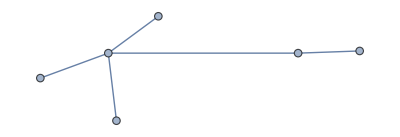
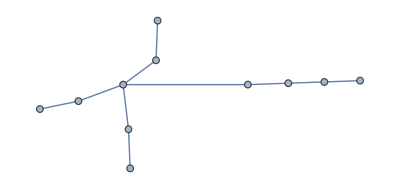
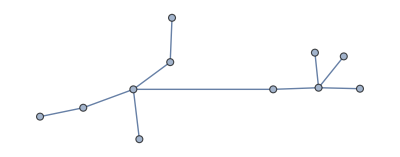
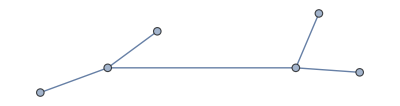
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
IsospectralPairs[treesten]  (* The suspects. *)
```

```mathematica
DeterminantD/@{-Graphics-,-Graphics-}//Simplify  (* Testing multiplicities *)
```

{-64 ⅇ^(-ⅈ k) (-9-6 ⅇ^((2 ⅈ k)/11)-5 ⅇ^((6 ⅈ k)/11)+2 ⅇ^((10 ⅈ k)/11)-2 ⅇ^((12 ⅈ k)/11)+5 ⅇ^((16 ⅈ k)/11)+6 ⅇ^((20 ⅈ k)/11)+9 ⅇ^(2 ⅈ k)),64 ⅇ^(-ⅈ k) (-9-6 ⅇ^((2 ⅈ k)/11)-5 ⅇ^((6 ⅈ k)/11)+2 ⅇ^((10 ⅈ k)/11)-2 ⅇ^((12 ⅈ k)/11)+5 ⅇ^((16 ⅈ k)/11)+6 ⅇ^((20 ⅈ k)/11)+9 ⅇ^(2 ⅈ k))}

```mathematica
Finalisospectraltreesten={{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}} (* The checked trees with up to twelve vertices *)
```

Here we do it for a decorated square.

```mathematica
treesfromsquare=PendantEdgeAddAll[-Graphics-,6]; (* Here we create a square decorated with edges and trees. *)
```

Below are the checked isospectral sets from a decorated square. There is one triplet and the rest are pairs. Note that the members of the pairs must be scaled to have the same length in order to be isospectral.

```mathematica
checkedsquarepairs=
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Here we do it for a decorated hexagon .

```mathematica
treesfromhexagon=PendantEdgeAddAll[-Graphics-,6];
```

Below are the checked decorated hexagon isospectral sets. I found one triplet and the rest are pairs.

```mathematica
checkedhexagonpairs={{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}.{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Below are checked isospectral pairs from this decorated graph - -Graphics-which was decorated with at most six edges.

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

Below are checked isospectral pairs from this decorated graph - -Graphics-which was decorated with at most five edges.

```mathematica
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
```

## The following cells check the isospectrality of one pair and one triplet from the paper which we do “by hand” in order to check the programs predictions.

The following cell gives the vertex and edge scattering matrix for graph b): -Graphics-which is the isospectral partner of the loop graph when L1=L3=1/4 and L2=2/4 according to Pistol, arXiv.
It also computes ∑(k) following Berkolaiko which shows that graph b) has the same eigenfrequencies as graph a).

```mathematica
L1=L3=2;
L2=4;
Sv=({{0, -1/2, 1/2, 1/2, 0, 1/2}, {1, 0, 0, 0, 0, 0}, {0, 1/2, 1/2, -1/2, 0, 1/2}, {0, 1/2, -1/2, 1/2, 0, 1/2}, {0, 1/2, 1/2, 1/2, 0, -1/2}, {0, 0, 0, 0, 1, 0}});
Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L2), 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L3), 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L3)}});
Id=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify
Sigma[k] (* The secular determinant *)

(* Here we do it again but with an extra valence two vertex on the left side of the loop to check *)
Sv=({{0, -1/2, 1/2, 0, 0, 1/2, 0, 1/2}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 1/2, -1/2, 0, 0, 1/2, 0, 1/2}, {0, 1/2, 1/2, 0, 0, -1/2, 0, 1/2}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 1/2, 1/2, 0, 0, 1/2, 0, -1/2}, {0, 0, 0, 1, 0, 0, 0, 0}});

Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L1), 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L1), 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L1), 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L1), 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L1)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify;
Sigma[k]

L1=4;L2=4;
Det[({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})-({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}).({{ⅇ^(ⅈ k L1), 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0}, {0, 0, 0, ⅇ^(ⅈ k L2)}})]//Simplify (* The loop with two vertices. The secular determinant *)
DeterminantD[-Graphics-]//Simplify (* The same secular determinant apart from a factor which never gives a root *)
(* Solve[Sigma[k]==0,k]   The eigenfrequencies according to the handcalculated Sv and Se *)
GraphRoots[-Graphics-] (* The same eigenfrequencies according to my program. *)
Sv=({{0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0}, {0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0}, {0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0}});(*-Graphics-*)
Se[k_]:=({{ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k 2), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k 1)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
Sigma[k_]:=Det[Id-Sv.Se[k]]//Simplify;
Sigma[k]
```

(-1+ⅇ^(8 ⅈ k))^2

(-1+ⅇ^(8 ⅈ k))^2

(-1+ⅇ^(8 ⅈ k))^2

-8 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2

{{k→ConditionalExpression[6 π C[1], C[1]∈ℤ]},{k→ConditionalExpression[2 π (-1+3 C[1]), C[1]∈ℤ]},{k→ConditionalExpression[2 (π+3 π C[1]), C[1]∈ℤ]}}

(-1+ⅇ^(8 ⅈ k))^2

The following cell shows that the graphs -Graphics-have the same secular determinant.

```mathematica
nn=nnm;
Subscript[L, 1]=nn;Subscript[L, 2]=1;Subscript[L, 3]=1;
sum=(Subscript[L, 1]+2 Subscript[L, 2]+2 Subscript[L, 3]);


Sv=({{0, -1/3, 2/3, 0, 2/3, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 0, 1/2, 1/2, 0, 1/2, 0}, {0, 2/3, -1/3, 0, 2/3, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, 0, -1/2, 1/2, 0, 1/2, 0}, {0, 2/3, 2/3, 0, -1/3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1/2, 0, 1/2, -1/2, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1/2, 0, 1/2, 1/2, 0, -1/2, 0}});  (* This is for -Graphics-*)
Se[k_]:=({{ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3]), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k Subscript[L, 3])}})
Id=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
Det[Id-Sv.Se[k]]//Simplify

Subscript[L, 1]=nn;Subscript[L, 2]=4;

Sv=({{0, -1/3, 2/3, 2/3}, {1, 0, 0, 0}, {0, 2/3, 2/3, -1/3}, {0, 2/3, -1/3, 2/3}});   (* This for-Graphics- *)
Se[k_]:=({{ⅇ^(ⅈ k Subscript[L, 1]), 0, 0, 0}, {0, ⅇ^(ⅈ k Subscript[L, 1]), 0, 0}, {0, 0, ⅇ^(ⅈ k Subscript[L, 2]), 0}, {0, 0, 0, ⅇ^(ⅈ k Subscript[L, 2])}});
Id=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Det[Id-Sv.Se[k]]//Simplify
```

1/3 (-1+ⅇ^(4 ⅈ k)) (-3+ⅇ^(4 ⅈ k)-ⅇ^(2 ⅈ k nnm)+3 ⅇ^(2 ⅈ k (2+nnm)))

1/3 (-1+ⅇ^(4 ⅈ k)) (-3+ⅇ^(4 ⅈ k)-ⅇ^(2 ⅈ k nnm)+3 ⅇ^(2 ⅈ k (2+nnm)))

The following cell finds the secular determinant of -Graphics-by hand which agrees with the results of the program (apart from this factor which never contributes a root).

```mathematica
k=.
L1=4;
L2=2;
L3=2;
L4:=L1-L3;
Sv=({{2/3, -1/3, 2/3, 0, 0, 0, 0, 0}, {-1/3, 2/3, 2/3, 0, 0, 0, 0, 0}, {0, 0, 0, -1/3, 2/3, 0, 2/3, 0}, {2/3, 2/3, -1/3, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 2/3, -1/3, 0, 2/3, 0}, {0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 2/3, 2/3, 0, -1/3, 0}}); (* This is the bondscattering matrix I get *)

Se[k_]:=({{ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0, 0}, {0, ⅇ^(ⅈ k L1), 0, 0, 0, 0, 0, 0}, {0, 0, ⅇ^(ⅈ k L2), 0, 0, 0, 0, 0}, {0, 0, 0, ⅇ^(ⅈ k L2), 0, 0, 0, 0}, {0, 0, 0, 0, ⅇ^(ⅈ k L3), 0, 0, 0}, {0, 0, 0, 0, 0, ⅇ^(ⅈ k L3), 0, 0}, {0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L4), 0}, {0, 0, 0, 0, 0, 0, 0, ⅇ^(ⅈ k L4)}});
Id=({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
Se[k];
Det[Id-Sv.Se[k]]//Simplify                                        (* What the handcalculation gets*)
Sigma[k_]:=Det[Id-Sv.Se[k]]//FullSimplify;
Sigma[k];
DeterminantD[#,10]&@-Graphics-//Simplify (* What my program gets*)
```

1/9 (-1+ⅇ^(4 ⅈ k))^2 (9+11 ⅇ^(4 ⅈ k)+11 ⅇ^(8 ⅈ k)+9 ⅇ^(12 ⅈ k))

64 ⅇ^(-10 ⅈ k) (-1+ⅇ^(4 ⅈ k))^2 (9+11 ⅇ^(4 ⅈ k)+11 ⅇ^(8 ⅈ k)+9 ⅇ^(12 ⅈ k))

Here we test the two isospectral partners of the loop

```mathematica
conn=-Graphics-;
DeterminantD/@{-Graphics-,-Graphics-,-Graphics-}//Simplify
h4=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];
h5=VertexReplace[-Graphics-,Table[i->Subscript[b, i],{i,25}]];
h6=VertexReplace[-Graphics-,Table[i->Subscript[c, i],{i,25}]];
{GraphPlot[h4,VertexLabels->"Name"],
GraphPlot[h5,VertexLabels->"Name"],
GraphPlot[h6,VertexLabels->"Name"]}

hx=GraphAddContract[h4,Allconnected⟦7⟧,Subscript[a, 3],2];
hy=GraphAddContract[h5,Allconnected⟦7⟧,Subscript[b, 3],2];
hx=Graph[hx,EdgeWeight->{1<->6->1}];
hy=Graph[hy,EdgeWeight->{1<->6->1}];
hz=GraphAddContract[h6,Allconnected⟦7⟧,Subscript[c, 1],1];
hw=GraphAddContract[h6,Allconnected⟦7⟧,Subscript[c, 3],1];
(DeterminantD[hx]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hy]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hz]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[hw]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
{GraphPlot[hx,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[hy,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]};
```

{256 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2,128 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2,16384 ⅇ^(-ⅈ k) (-1+ⅇ^(ⅈ k))^2}

{-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^((ⅈ k)/16))^5 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^3 (20+40 ⅇ^((ⅈ k)/16)+55 ⅇ^((ⅈ k)/8)+50 ⅇ^((3 ⅈ k)/16)+71 ⅇ^((ⅈ k)/4)+88 ⅇ^((5 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/8)+82 ⅇ^((7 ⅈ k)/16)+91 ⅇ^((ⅈ k)/2)+96 ⅇ^((9 ⅈ k)/16)+91 ⅇ^((5 ⅈ k)/8)+82 ⅇ^((11 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/4)+88 ⅇ^((13 ⅈ k)/16)+71 ⅇ^((7 ⅈ k)/8)+50 ⅇ^((15 ⅈ k)/16)+55 ⅇ^(ⅈ k)+40 ⅇ^((17 ⅈ k)/16)+20 ⅇ^((9 ⅈ k)/8))

(-1+ⅇ^((ⅈ k)/16))^5 (1+ⅇ^((ⅈ k)/16)+ⅇ^((ⅈ k)/8)+ⅇ^((3 ⅈ k)/16))^3 (20+40 ⅇ^((ⅈ k)/16)+55 ⅇ^((ⅈ k)/8)+50 ⅇ^((3 ⅈ k)/16)+71 ⅇ^((ⅈ k)/4)+88 ⅇ^((5 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/8)+82 ⅇ^((7 ⅈ k)/16)+91 ⅇ^((ⅈ k)/2)+96 ⅇ^((9 ⅈ k)/16)+91 ⅇ^((5 ⅈ k)/8)+82 ⅇ^((11 ⅈ k)/16)+95 ⅇ^((3 ⅈ k)/4)+88 ⅇ^((13 ⅈ k)/16)+71 ⅇ^((7 ⅈ k)/8)+50 ⅇ^((15 ⅈ k)/16)+55 ⅇ^(ⅈ k)+40 ⅇ^((17 ⅈ k)/16)+20 ⅇ^((9 ⅈ k)/8))

(-1+ⅇ^((ⅈ k)/24))^5 (1+ⅇ^((ⅈ k)/24)+ⅇ^((ⅈ k)/12)+ⅇ^((ⅈ k)/8))^3 (1+ⅇ^((ⅈ k)/6))^2 (30+60 ⅇ^((ⅈ k)/24)+77 ⅇ^((ⅈ k)/12)+66 ⅇ^((ⅈ k)/8)+49 ⅇ^((ⅈ k)/6)+36 ⅇ^((5 ⅈ k)/24)+26 ⅇ^((ⅈ k)/4)+32 ⅇ^((7 ⅈ k)/24)+94 ⅇ^((ⅈ k)/3)+140 ⅇ^((3 ⅈ k)/8)+141 ⅇ^((5 ⅈ k)/12)+98 ⅇ^((11 ⅈ k)/24)+75 ⅇ^((ⅈ k)/2)+72 ⅇ^((13 ⅈ k)/24)+75 ⅇ^((7 ⅈ k)/12)+98 ⅇ^((5 ⅈ k)/8)+141 ⅇ^((2 ⅈ k)/3)+140 ⅇ^((17 ⅈ k)/24)+94 ⅇ^((3 ⅈ k)/4)+32 ⅇ^((19 ⅈ k)/24)+26 ⅇ^((5 ⅈ k)/6)+36 ⅇ^((7 ⅈ k)/8)+49 ⅇ^((11 ⅈ k)/12)+66 ⅇ^((23 ⅈ k)/24)+77 ⅇ^(ⅈ k)+60 ⅇ^((25 ⅈ k)/24)+30 ⅇ^((13 ⅈ k)/12))

(-1+ⅇ^((ⅈ k)/24))^5 (1+ⅇ^((ⅈ k)/24)+ⅇ^((ⅈ k)/12)+ⅇ^((ⅈ k)/8))^3 (1+ⅇ^((ⅈ k)/3))^2 (30+60 ⅇ^((ⅈ k)/24)+77 ⅇ^((ⅈ k)/12)+66 ⅇ^((ⅈ k)/8)+99 ⅇ^((ⅈ k)/6)+136 ⅇ^((5 ⅈ k)/24)+147 ⅇ^((ⅈ k)/4)+130 ⅇ^((7 ⅈ k)/24)+139 ⅇ^((ⅈ k)/3)+152 ⅇ^((3 ⅈ k)/8)+139 ⅇ^((5 ⅈ k)/12)+130 ⅇ^((11 ⅈ k)/24)+147 ⅇ^((ⅈ k)/2)+136 ⅇ^((13 ⅈ k)/24)+99 ⅇ^((7 ⅈ k)/12)+66 ⅇ^((5 ⅈ k)/8)+77 ⅇ^((2 ⅈ k)/3)+60 ⅇ^((17 ⅈ k)/24)+30 ⅇ^((3 ⅈ k)/4))

## Experiments with the star graph

Here we test the isospectrality of the decorated star. We first do it for a star with equal length of the leaves.

```mathematica
star=.;loop1=.;loop2=.;v1=.;v2=.;u=.;v=.;
v=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];
star=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];

loop1=VertexReplace[-Graphics-,Table[i->Subscript[b1, i],{i,25}]];loop2=VertexReplace[-Graphics-,Table[i->Subscript[b2, i],{i,25}]];
loop3=VertexReplace[-Graphics-,Table[i->Subscript[b3, i],{i,25}]];


v1=VertexReplace[v,Table[i->Subscript[d1, i],{i,25}]];
v2=VertexReplace[v,Table[i->Subscript[d2, i],{i,25}]];
v3=VertexReplace[v,Table[i->Subscript[d3, i],{i,25}]];


{decoratedstar1=VertexReplace[#,atable]&@IndexGraph@GraphAddContract3[star,loop1,loop2,loop3,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[b3, 1]],
decoratedstar2=VertexReplace[#,btable]&@IndexGraph@GraphAddContract3[star,loop1,loop2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[d1, 2]],
decoratedstar3=VertexReplace[#,ctable]&@IndexGraph@GraphAddContract3[star,loop1,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[d2, 2],Subscript[d1, 2]],
decoratedstar4=VertexReplace[#,dtable]&@IndexGraph@GraphAddContract3[star,v3,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[d3, 2],Subscript[d2, 2],Subscript[d1, 2]]}


(DeterminantD[decoratedstar1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[decoratedstar4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

(-1+ⅇ^(2 ⅈ))^4 (1+ⅇ^(2 ⅈ))^5 (1+ⅇ^(4 ⅈ))^3 (3-4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)-4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))^2 (3+4 ⅇ^(2 ⅈ)+4 ⅇ^(4 ⅈ)+4 ⅇ^(6 ⅈ)+3 ⅇ^(8 ⅈ))

«1 more identical outputs»

We then do it for a star with symbolic edgelengths.

```mathematica
c1=.;c2=.;
longstar=Graph[{1<->12,12<->2,1<->13,13<->3,1<->14,14<->4}];
longstar=VertexReplace[-Graphics-,Table[i->Subscript[a, i],{i,25}]];

{decoratedlongstar1=VertexReplace[#,atable]&@IndexGraph@GraphAddContract3[longstar,loop1,loop2,loop3,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[b3, 1]],
decoratedlongstar2=VertexReplace[#,btable]&@IndexGraph@GraphAddContract3[longstar,loop1,loop2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[b2, 1],Subscript[d1, 2]],
decoratedlongstar3=VertexReplace[#,ctable]&@IndexGraph@GraphAddContract3[longstar,loop1,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b1, 1],Subscript[d2, 2],Subscript[d1, 2]],
decoratedlongstar4=VertexReplace[#,dtable]&@IndexGraph@GraphAddContract3[longstar,v3,v2,v1,Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[d3, 2],Subscript[d2, 2],Subscript[d1, 2]]};

decoratedlongstar1=VertexReplace[#,atable]&@IndexGraph@Graph[decoratedlongstar1,EdgeWeight->{Subscript[a, 1]<->Subscript[a, 2]->c1,Subscript[a, 1]<->Subscript[a, 3]->c2}];
decoratedlongstar2=VertexReplace[#,btable]&@IndexGraph@Graph[decoratedlongstar2,EdgeWeight->{Subscript[b, 1]<->Subscript[b, 2]->c1,Subscript[b, 1]<->Subscript[b, 3]->c2}];
decoratedlongstar3=VertexReplace[#,ctable]&@IndexGraph@Graph[decoratedlongstar3,EdgeWeight->{Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[c, 1]<->Subscript[c, 3]->c2}];
decoratedlongstar4=VertexReplace[#,dtable]&@IndexGraph@Graph[decoratedlongstar4,EdgeWeight->{Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[d, 1]<->Subscript[d, 3]->c2}];

{GraphPlot[decoratedlongstar1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar3,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],
GraphPlot[decoratedlongstar4,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}

x1=(DeterminantD[decoratedlongstar1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x2=(DeterminantD[decoratedlongstar2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x3=(DeterminantD[decoratedlongstar3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
x4=(DeterminantD[decoratedlongstar4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
{x1==x2,x1==x3,x1==x4}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

(-1+ⅇ^((216 ⅈ)/(28+c1+c2)))^3 (-81+9 ⅇ^((108 ⅈ)/(28+c1+c2))+81 ⅇ^((216 ⅈ)/(28+c1+c2))-33 ⅇ^((324 ⅈ)/(28+c1+c2))-27 ⅇ^((432 ⅈ)/(28+c1+c2))+19 ⅇ^((540 ⅈ)/(28+c1+c2))+3 ⅇ^((648 ⅈ)/(28+c1+c2))-3 ⅇ^((756 ⅈ)/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c1))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c1))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c1))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c1))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c1))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c1))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c1))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c1))/(28+c1+c2))+9 ⅇ^((54 ⅈ (1+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (3+c2))/(28+c1+c2))-33 ⅇ^((54 ⅈ (5+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (7+c2))/(28+c1+c2))+19 ⅇ^((54 ⅈ (9+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (11+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (13+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (15+c2))/(28+c1+c2))+3 ⅇ^((54 ⅈ (2+c1+c2))/(28+c1+c2))-3 ⅇ^((54 ⅈ (4+c1+c2))/(28+c1+c2))-19 ⅇ^((54 ⅈ (6+c1+c2))/(28+c1+c2))+27 ⅇ^((54 ⅈ (8+c1+c2))/(28+c1+c2))+33 ⅇ^((54 ⅈ (10+c1+c2))/(28+c1+c2))-81 ⅇ^((54 ⅈ (12+c1+c2))/(28+c1+c2))-9 ⅇ^((54 ⅈ (14+c1+c2))/(28+c1+c2))+81 ⅇ^((54 ⅈ (16+c1+c2))/(28+c1+c2)))

«1 more identical outputs»

{True,True,True}

And finally lets attach graphs at possible hot vertices. If c1 or c2 are not 1 there are no hot vertices.

```mathematica
c1=3;c2=2;
decoratedlongstar2attached1=Graph[#,EdgeWeight->{Subscript[b, 1]<->Subscript[b, 2]->c1,Subscript[b, 2]<->Subscript[b, 1]->c1,Subscript[b, 1]<->Subscript[b, 3]->c2,Subscript[b, 3]<->Subscript[b, 1]->c2}]&@GraphAddContract[decoratedlongstar2,Allconnected[[9]],Subscript[b, 26],1];
decoratedlongstar3attached1=Graph[#,EdgeWeight->{Subscript[c, 1]<->Subscript[c, 2]->c1,Subscript[c, 2]<->Subscript[c, 1]->c1,Subscript[c, 1]<->Subscript[c, 3]->c2,Subscript[c, 3]<->Subscript[c, 1]->c2}]&@GraphAddContract[decoratedlongstar3,Allconnected[[9]],Subscript[c, 27],1];
decoratedlongstar4attached1=Graph[#,EdgeWeight->{Subscript[d, 1]<->Subscript[d, 2]->c1,Subscript[d, 2]<->Subscript[d, 1]->c1,Subscript[d, 1]<->Subscript[d, 3]->c2,Subscript[d, 3]<->Subscript[d, 1]->c2}]&@GraphAddContract[decoratedlongstar4,Allconnected[[9]],Subscript[d, 28],1];

GraphPlot[decoratedlongstar2attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];
GraphPlot[decoratedlongstar3attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];
GraphPlot[decoratedlongstar4attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];

{GraphPlot[decoratedlongstar2attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x1=(DeterminantD[decoratedlongstar2attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{GraphPlot[decoratedlongstar3attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x2=(DeterminantD[decoratedlongstar3attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{GraphPlot[decoratedlongstar4attached1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],x3=(DeterminantD[decoratedlongstar4attached1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}}
{x1==x2,x1==x3}
GraphPlot[decoratedlongstar2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];  (* 26, 27, 28 are hot vertices, 2, 3, 4 are also hot vertices from the second set. *)   
None;
```

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2625 ⅇ^((27 ⅈ)/10)+2550 ⅇ^((27 ⅈ)/8)+2355 ⅇ^((81 ⅈ)/20)+2136 ⅇ^((189 ⅈ)/40)+1788 ⅇ^((27 ⅈ)/5)+1572 ⅇ^((243 ⅈ)/40)+944 ⅇ^((27 ⅈ)/4)+736 ⅇ^((297 ⅈ)/40)+799 ⅇ^((81 ⅈ)/10)+902 ⅇ^((351 ⅈ)/40)+1077 ⅇ^((189 ⅈ)/20)+724 ⅇ^((81 ⅈ)/8)+817 ⅇ^((54 ⅈ)/5)+666 ⅇ^((459 ⅈ)/40)+865 ⅇ^((243 ⅈ)/20)+1104 ⅇ^((513 ⅈ)/40)+1674 ⅇ^((27 ⅈ)/2)+2372 ⅇ^((567 ⅈ)/40)+2990 ⅇ^((297 ⅈ)/20)+3784 ⅇ^((621 ⅈ)/40)+4628 ⅇ^((81 ⅈ)/5)+4984 ⅇ^((135 ⅈ)/8)+4628 ⅇ^((351 ⅈ)/20)+3784 ⅇ^((729 ⅈ)/40)+2990 ⅇ^((189 ⅈ)/10)+2372 ⅇ^((783 ⅈ)/40)+1674 ⅇ^((81 ⅈ)/4)+1104 ⅇ^((837 ⅈ)/40)+865 ⅇ^((108 ⅈ)/5)+666 ⅇ^((891 ⅈ)/40)+817 ⅇ^((459 ⅈ)/20)+724 ⅇ^((189 ⅈ)/8)+1077 ⅇ^((243 ⅈ)/10)+902 ⅇ^((999 ⅈ)/40)+799 ⅇ^((513 ⅈ)/20)+736 ⅇ^((1053 ⅈ)/40)+944 ⅇ^(27 ⅈ)+1572 ⅇ^((1107 ⅈ)/40)+1788 ⅇ^((567 ⅈ)/20)+2136 ⅇ^((1161 ⅈ)/40)+2355 ⅇ^((297 ⅈ)/10)+2550 ⅇ^((243 ⅈ)/8)+2625 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2625 ⅇ^((27 ⅈ)/10)+2550 ⅇ^((27 ⅈ)/8)+2295 ⅇ^((81 ⅈ)/20)+2016 ⅇ^((189 ⅈ)/40)+1632 ⅇ^((27 ⅈ)/5)+1476 ⅇ^((243 ⅈ)/40)+864 ⅇ^((27 ⅈ)/4)+672 ⅇ^((297 ⅈ)/40)+807 ⅇ^((81 ⅈ)/10)+1014 ⅇ^((351 ⅈ)/40)+1113 ⅇ^((189 ⅈ)/20)+588 ⅇ^((81 ⅈ)/8)+637 ⅇ^((54 ⅈ)/5)+602 ⅇ^((459 ⅈ)/40)+837 ⅇ^((243 ⅈ)/20)+1080 ⅇ^((513 ⅈ)/40)+1846 ⅇ^((27 ⅈ)/2)+2708 ⅇ^((567 ⅈ)/40)+3250 ⅇ^((297 ⅈ)/20)+3808 ⅇ^((621 ⅈ)/40)+4656 ⅇ^((81 ⅈ)/5)+5048 ⅇ^((135 ⅈ)/8)+4656 ⅇ^((351 ⅈ)/20)+3808 ⅇ^((729 ⅈ)/40)+3250 ⅇ^((189 ⅈ)/10)+2708 ⅇ^((783 ⅈ)/40)+1846 ⅇ^((81 ⅈ)/4)+1080 ⅇ^((837 ⅈ)/40)+837 ⅇ^((108 ⅈ)/5)+602 ⅇ^((891 ⅈ)/40)+637 ⅇ^((459 ⅈ)/20)+588 ⅇ^((189 ⅈ)/8)+1113 ⅇ^((243 ⅈ)/10)+1014 ⅇ^((999 ⅈ)/40)+807 ⅇ^((513 ⅈ)/20)+672 ⅇ^((1053 ⅈ)/40)+864 ⅇ^(27 ⅈ)+1476 ⅇ^((1107 ⅈ)/40)+1632 ⅇ^((567 ⅈ)/20)+2016 ⅇ^((1161 ⅈ)/40)+2295 ⅇ^((297 ⅈ)/10)+2550 ⅇ^((243 ⅈ)/8)+2625 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{-Graphics-,(-1+ⅇ^((27 ⅈ)/40))^6 (1+ⅇ^((27 ⅈ)/40)+ⅇ^((27 ⅈ)/20)+ⅇ^((81 ⅈ)/40))^4 (1+ⅇ^((27 ⅈ)/10))^3 (675+1350 ⅇ^((27 ⅈ)/40)+2187 ⅇ^((27 ⅈ)/20)+2268 ⅇ^((81 ⅈ)/40)+2565 ⅇ^((27 ⅈ)/10)+2430 ⅇ^((27 ⅈ)/8)+2139 ⅇ^((81 ⅈ)/20)+1920 ⅇ^((189 ⅈ)/40)+1572 ⅇ^((27 ⅈ)/5)+1452 ⅇ^((243 ⅈ)/40)+924 ⅇ^((27 ⅈ)/4)+816 ⅇ^((297 ⅈ)/40)+843 ⅇ^((81 ⅈ)/10)+846 ⅇ^((351 ⅈ)/40)+861 ⅇ^((189 ⅈ)/20)+444 ⅇ^((81 ⅈ)/8)+517 ⅇ^((54 ⅈ)/5)+506 ⅇ^((459 ⅈ)/40)+957 ⅇ^((243 ⅈ)/20)+1416 ⅇ^((513 ⅈ)/40)+2158 ⅇ^((27 ⅈ)/2)+2804 ⅇ^((567 ⅈ)/40)+3370 ⅇ^((297 ⅈ)/20)+3952 ⅇ^((621 ⅈ)/40)+4656 ⅇ^((81 ⅈ)/5)+4904 ⅇ^((135 ⅈ)/8)+4656 ⅇ^((351 ⅈ)/20)+3952 ⅇ^((729 ⅈ)/40)+3370 ⅇ^((189 ⅈ)/10)+2804 ⅇ^((783 ⅈ)/40)+2158 ⅇ^((81 ⅈ)/4)+1416 ⅇ^((837 ⅈ)/40)+957 ⅇ^((108 ⅈ)/5)+506 ⅇ^((891 ⅈ)/40)+517 ⅇ^((459 ⅈ)/20)+444 ⅇ^((189 ⅈ)/8)+861 ⅇ^((243 ⅈ)/10)+846 ⅇ^((999 ⅈ)/40)+843 ⅇ^((513 ⅈ)/20)+816 ⅇ^((1053 ⅈ)/40)+924 ⅇ^(27 ⅈ)+1452 ⅇ^((1107 ⅈ)/40)+1572 ⅇ^((567 ⅈ)/20)+1920 ⅇ^((1161 ⅈ)/40)+2139 ⅇ^((297 ⅈ)/10)+2430 ⅇ^((243 ⅈ)/8)+2565 ⅇ^((621 ⅈ)/20)+2268 ⅇ^((1269 ⅈ)/40)+2187 ⅇ^((162 ⅈ)/5)+1350 ⅇ^((1323 ⅈ)/40)+675 ⅇ^((135 ⅈ)/4))}

{False,False}

Here we test the isospectral pairs -Graphics- and-Graphics-for hot vertices.

```mathematica
u=.;v=.;s=.;t=.;
u=CirculantGraph[8,1];
v=Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)

s=Graph[{1<->2,2<->3,3<->4,4<->5,3<->6,6<->7,7<->8,8<->9,9<->10,10<->7}];
t=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->3,5<->7,7<->8,8<->9,9<->10}]; (* s = -Graphics- and t = -Graphics- are the other two isospectral partners. *)

u=VertexReplace[u,Table[i->Subscript[a, i],{i,55}]];  (* This is a loop. Hot vertices are all of them, Subscript[a, 1]-Subscript[a, 8] *)
v=VertexReplace[v,Table[i->Subscript[b, i],{i,55}]]; (* Hot vertex is Subscript[b, 2] -Graphics-*)
s=VertexReplace[s,Table[i->Subscript[c, i],{i,55}]]; (* Hot vertices are Subscript[c, 3] and Subscript[c, 7] -Graphics- *)
t=VertexReplace[t,Table[i->Subscript[d, i],{i,55}]]; (* Hot vertex is Subscript[d, 3] -Graphics- *)
w1=Allconnected⟦151⟧;
GraphPlot[w1,VertexLabels->"Name"];
w1=VertexReplace[w1,Table[i->Subscript[e, i],{i,25}]];

h1=GraphAddContract[u,w1,Subscript[a, 1],Subscript[e, 5]];
h2=GraphAddContract[v,w1,Subscript[b, 2],Subscript[e, 5]];

h3=GraphAddContract[s,w1,Subscript[c, 7],Subscript[e, 2]];
h4=GraphAddContract[t,w1,Subscript[d, 3],Subscript[e, 2]];
h5=GraphAddContract[s,w1,Subscript[c, 3],Subscript[e, 2]];
h6=GraphAddContract[t,w1,Subscript[d, 5],Subscript[e, 2]];(* Subscript[d, 5] does not work *)

g=GraphAddContract[u,v,Subscript[a, 1],Subscript[e, 2]];
GraphPlot[s,EdgeLabels->"EdgeWeight",VertexLabels->"Name"];
GraphPlot[t,EdgeLabels->"EdgeWeight",VertexLabels->"Name"];
DeterminantD[s]//Simplify;
DeterminantD[t]//Simplify;
(DeterminantD[h1]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
(DeterminantD[h2]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
Print["next set"]
xx1=(DeterminantD[h3]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx2=(DeterminantD[h4]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx3=(DeterminantD[h5]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1}
xx4=(DeterminantD[h6]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
(DeterminantD[h6]//Simplify)/.{_Integer ⅇ^(-ⅈ k) -> 1};
{xx1==xx2,xx1==xx3}
```

(-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16))^2 (1+ⅇ^((ⅈ k)/8))^3 (15+30 ⅇ^((ⅈ k)/16)+33 ⅇ^((ⅈ k)/8)+24 ⅇ^((3 ⅈ k)/16)+39 ⅇ^((ⅈ k)/4)+62 ⅇ^((5 ⅈ k)/16)+74 ⅇ^((3 ⅈ k)/8)+62 ⅇ^((7 ⅈ k)/16)+62 ⅇ^((ⅈ k)/2)+70 ⅇ^((9 ⅈ k)/16)+82 ⅇ^((5 ⅈ k)/8)+70 ⅇ^((11 ⅈ k)/16)+62 ⅇ^((3 ⅈ k)/4)+62 ⅇ^((13 ⅈ k)/16)+74 ⅇ^((7 ⅈ k)/8)+62 ⅇ^((15 ⅈ k)/16)+39 ⅇ^(ⅈ k)+24 ⅇ^((17 ⅈ k)/16)+33 ⅇ^((9 ⅈ k)/8)+30 ⅇ^((19 ⅈ k)/16)+15 ⅇ^((5 ⅈ k)/4))

(-1+ⅇ^((ⅈ k)/16))^4 (1+ⅇ^((ⅈ k)/16))^2 (1+ⅇ^((ⅈ k)/8))^3 (15+30 ⅇ^((ⅈ k)/16)+33 ⅇ^((ⅈ k)/8)+24 ⅇ^((3 ⅈ k)/16)+39 ⅇ^((ⅈ k)/4)+62 ⅇ^((5 ⅈ k)/16)+74 ⅇ^((3 ⅈ k)/8)+62 ⅇ^((7 ⅈ k)/16)+62 ⅇ^((ⅈ k)/2)+70 ⅇ^((9 ⅈ k)/16)+82 ⅇ^((5 ⅈ k)/8)+70 ⅇ^((11 ⅈ k)/16)+62 ⅇ^((3 ⅈ k)/4)+62 ⅇ^((13 ⅈ k)/16)+74 ⅇ^((7 ⅈ k)/8)+62 ⅇ^((15 ⅈ k)/16)+39 ⅇ^(ⅈ k)+24 ⅇ^((17 ⅈ k)/16)+33 ⅇ^((9 ⅈ k)/8)+30 ⅇ^((19 ⅈ k)/16)+15 ⅇ^((5 ⅈ k)/4))

next set

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

(-1+ⅇ^((ⅈ k)/18))^4 (1+ⅇ^((ⅈ k)/18))^2 (1+ⅇ^((ⅈ k)/9))^3 (270+540 ⅇ^((ⅈ k)/18)+495 ⅇ^((ⅈ k)/9)+198 ⅇ^((ⅈ k)/6)+420 ⅇ^((2 ⅈ k)/9)+1026 ⅇ^((5 ⅈ k)/18)+1263 ⅇ^((ⅈ k)/3)+672 ⅇ^((7 ⅈ k)/18)+466 ⅇ^((4 ⅈ k)/9)+1028 ⅇ^((ⅈ k)/2)+1506 ⅇ^((5 ⅈ k)/9)+1016 ⅇ^((11 ⅈ k)/18)+632 ⅇ^((2 ⅈ k)/3)+1016 ⅇ^((13 ⅈ k)/18)+1506 ⅇ^((7 ⅈ k)/9)+1028 ⅇ^((5 ⅈ k)/6)+466 ⅇ^((8 ⅈ k)/9)+672 ⅇ^((17 ⅈ k)/18)+1263 ⅇ^(ⅈ k)+1026 ⅇ^((19 ⅈ k)/18)+420 ⅇ^((10 ⅈ k)/9)+198 ⅇ^((7 ⅈ k)/6)+495 ⅇ^((11 ⅈ k)/9)+540 ⅇ^((23 ⅈ k)/18)+270 ⅇ^((4 ⅈ k)/3))

{True,True}

Here we take a graph, G, and attach -Graphics-with their hot vertices at different vertices of G in different permutations and check that the resulting graphs are isospectral.

```mathematica
G=VertexReplace[#,ctable]&@Allconnected[[39]];
u1=VertexReplace[#,atable]&@CirculantGraph[8,1];
u2=VertexReplace[#,ftable]&@CirculantGraph[8,1];
v1=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];v3=VertexReplace[#,etable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];GraphPlot[v,VertexLabels->"Name"];  (* Hot vertex is Subscript[b, 2] -Graphics- *)
Gdecorated1=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated2=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 2],Subscript[c, 1],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated3=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 3],Subscript[c, 2],Subscript[c, 1],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]
Gdecorated4=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]]  
Gdecorated5=GraphAddContract4[G,u1,u2,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[f, 2],Subscript[d, 2],Subscript[e, 2]]  
Gdecorated6=GraphAddContract4[G,u1,v1,u2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[f, 2],Subscript[e, 2]]  

GraphPlot[G,VertexLabels->"Name"]
GraphPlot[Gdecorated1,VertexLabels->"Name"]

x1=(DeterminantD@Gdecorated1//Simplify)/.{_Integer -> 1}
x2=(DeterminantD@Gdecorated2//Simplify)/.{_Integer -> 1}
x3=(DeterminantD@Gdecorated3//Simplify)/.{_Integer -> 1}
x4=(DeterminantD@Gdecorated4//Simplify)/.{_Integer -> 1}
x5=(DeterminantD@Gdecorated5//Simplify)/.{_Integer -> 1}
x6=(DeterminantD@Gdecorated6//Simplify)/.{_Integer -> 1}
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

(1+ⅇ^((6 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)) (1+ⅇ^((24 ⅈ)/5)) (1+ⅇ^((6 ⅈ)/5)+ⅇ^((12 ⅈ)/5)+ⅇ^((18 ⅈ)/5)+ⅇ^((24 ⅈ)/5)+ⅇ^(6 ⅈ)+ⅇ^((36 ⅈ)/5)+ⅇ^((42 ⅈ)/5)+ⅇ^((48 ⅈ)/5)+ⅇ^((54 ⅈ)/5)+ⅇ^(12 ⅈ)+ⅇ^((66 ⅈ)/5)+ⅇ^((72 ⅈ)/5)+ⅇ^((78 ⅈ)/5)+ⅇ^((84 ⅈ)/5)+ⅇ^(18 ⅈ)+ⅇ^((96 ⅈ)/5)+ⅇ^((102 ⅈ)/5)+ⅇ^((108 ⅈ)/5)+ⅇ^((114 ⅈ)/5)+ⅇ^(24 ⅈ)+ⅇ^((126 ⅈ)/5)+ⅇ^((132 ⅈ)/5)+ⅇ^((138 ⅈ)/5)+ⅇ^((144 ⅈ)/5)+ⅇ^(30 ⅈ)+ⅇ^((156 ⅈ)/5)+ⅇ^((162 ⅈ)/5)+ⅇ^((168 ⅈ)/5)+ⅇ^((174 ⅈ)/5)+ⅇ^(36 ⅈ)+ⅇ^((186 ⅈ)/5)+ⅇ^((192 ⅈ)/5)+ⅇ^((198 ⅈ)/5)+ⅇ^((204 ⅈ)/5)+ⅇ^(42 ⅈ)+ⅇ^((216 ⅈ)/5)+ⅇ^((222 ⅈ)/5)+ⅇ^((228 ⅈ)/5)) ⅇ^(-48 ⅈ)

«3 more identical outputs»

Let’s attach -Graphics-to many different graphs G.

```mathematica
Do[rnd=RandomInteger[{1,995}];
G=VertexReplace[#,ctable]&@Allconnected[[rnd]];
u1=VertexReplace[#,atable]&@CirculantGraph[8,1];
u2=VertexReplace[#,ftable]&@CirculantGraph[8,1];
v1=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (* u = -Graphics- and the isospectral partner is v = -Graphics-. *)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];v3=VertexReplace[#,etable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];GraphPlot[v,VertexLabels->"Name"];  (* Hot vertex is Subscript[b, 2] -Graphics- *)
Gdecorated1=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated2=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 2],Subscript[c, 1],Subscript[c, 3],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated3=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 3],Subscript[c, 2],Subscript[c, 1],Subscript[c, 4],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]];
Gdecorated4=GraphAddContract4[G,u1,v1,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[d, 2],Subscript[e, 2]] ;
Gdecorated5=GraphAddContract4[G,u1,u2,v2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[f, 2],Subscript[d, 2],Subscript[e, 2]] ;
Gdecorated6=GraphAddContract4[G,u1,v1,u2,v3,Subscript[c, 4],Subscript[c, 2],Subscript[c, 3],Subscript[c, 1],Subscript[a, 1],Subscript[b, 2],Subscript[f, 2],Subscript[e, 2]] ; 

GraphPlot[G,VertexLabels->"Name"];
GraphPlot[Gdecorated1,VertexLabels->"Name"];

x1=(DeterminantD@Gdecorated1//Simplify)/.{_Integer -> 1};
x2=(DeterminantD@Gdecorated2//Simplify)/.{_Integer -> 1};
x3=(DeterminantD@Gdecorated3//Simplify)/.{_Integer -> 1};
x4=(DeterminantD@Gdecorated4//Simplify)/.{_Integer -> 1};
x5=(DeterminantD@Gdecorated5//Simplify)/.{_Integer -> 1};
x6=(DeterminantD@Gdecorated6//Simplify)/.{_Integer -> 1};
WriteString["stdout",{x1==x2,x1==x3,x1==x4,x1==x5,x1==x6}," "],
{i,1,25}]
```

{True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True} {True, True, True, True, True}

## Let’s check if , and can generate isospectral graphs. They seem to form a generating set, being not isospectral, but still able to decorate symmetric graphs and generate hot vertices. The pair also is able to decorate general compact graphs generating isospectral graphs.

We first generate a set of graphs having a lot of symmetry, and the relevant graphs to attach.

```mathematica
(*CompleteGraph[5], WheelGraph[5],PetersenGraph[6,2],HararyGraph[5,10]*)
SymGraphs={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
G=VertexReplace[#,gtable]&@-Graphics-;
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  
w=VertexReplace[#,ctable]&@PathGraph[Range[9]] ; (* u = -Graphics- (with attachment vertex Subscript[a, 1]), v = -Graphics- (with attachment vertex Subscript[b, 3]) and w = -Graphics- (with attachment vertex Subscript[c, 5]). *)

GraphPlot[w,VertexLabels->"Name"];
w
```

-Graphics-

Let’s decorate a “random” graph with  , , and -Graphics-  in two ways and check if the resulting graphs are isospectral.

```mathematica
Gd=Allconnected[[995]];  (* Choose any graph ut to the maximum index of 995 *)

u1=VertexReplace[#,atable]&@CirculantGraph[8,1]; (*-Graphics-*)
u2=VertexReplace[#,btable]&@CirculantGraph[8,1];
v1=VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}] ; (*-Graphics-*)
v2=VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}] ;
w1=VertexReplace[#,etable]&@PathGraph[Range[9]]; (*-Graphics-*)
w2=VertexReplace[#,ftable]&@PathGraph[Range[9]];

h1=GraphAddContract2[Gd,w2,u1,1,2, Subscript[f, 5],Subscript[a, 3]];
h2=GraphAddContract2[Gd,w2,u1,2,1, Subscript[f, 5],Subscript[a, 3]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]}
{HighlightGraph[h1,{_Integer<->_Integer}], HighlightGraph[h2,{_Integer<->_Integer}]}
x1=(DeterminantD@h1)/.{_Integer -> 1}
x2=(DeterminantD@h2)/.{_Integer -> 1}   (* We need to do this to get rid of the sign problem. *)
x1==x2
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

ⅇ^(-(43 ⅈ k)/28) (ⅇ^((15 ⅈ k)/28)+ⅇ^((17 ⅈ k)/28)+ⅇ^((9 ⅈ k)/14)+ⅇ^((19 ⅈ k)/28)+ⅇ^((5 ⅈ k)/7)+ⅇ^((3 ⅈ k)/4)+ⅇ^((11 ⅈ k)/14)+ⅇ^((23 ⅈ k)/28)+ⅇ^((6 ⅈ k)/7)+ⅇ^((25 ⅈ k)/28)+ⅇ^((13 ⅈ k)/14)+ⅇ^((27 ⅈ k)/28)+ⅇ^(ⅈ k)+ⅇ^((29 ⅈ k)/28)+ⅇ^((15 ⅈ k)/14)+ⅇ^((31 ⅈ k)/28)+ⅇ^((8 ⅈ k)/7)+ⅇ^((33 ⅈ k)/28)+ⅇ^((17 ⅈ k)/14)+ⅇ^((5 ⅈ k)/4)+ⅇ^((9 ⅈ k)/7)+ⅇ^((37 ⅈ k)/28)+ⅇ^((19 ⅈ k)/14)+ⅇ^((39 ⅈ k)/28)+ⅇ^((10 ⅈ k)/7)+ⅇ^((41 ⅈ k)/28)+ⅇ^((3 ⅈ k)/2)+ⅇ^((43 ⅈ k)/28)+ⅇ^((11 ⅈ k)/7)+ⅇ^((45 ⅈ k)/28)+ⅇ^((23 ⅈ k)/14)+ⅇ^((47 ⅈ k)/28)+ⅇ^((12 ⅈ k)/7)+ⅇ^((7 ⅈ k)/4)+ⅇ^((25 ⅈ k)/14)+ⅇ^((51 ⅈ k)/28)+ⅇ^((13 ⅈ k)/7)+ⅇ^((53 ⅈ k)/28)+ⅇ^((27 ⅈ k)/14)+ⅇ^((55 ⅈ k)/28)+ⅇ^(2 ⅈ k)+ⅇ^((57 ⅈ k)/28)+ⅇ^((29 ⅈ k)/14)+ⅇ^((59 ⅈ k)/28)+ⅇ^((15 ⅈ k)/7)+ⅇ^((61 ⅈ k)/28)+ⅇ^((31 ⅈ k)/14)+ⅇ^((9 ⅈ k)/4)+ⅇ^((16 ⅈ k)/7)+ⅇ^((65 ⅈ k)/28)+ⅇ^((33 ⅈ k)/14)+ⅇ^((67 ⅈ k)/28)+ⅇ^((17 ⅈ k)/7)+ⅇ^((69 ⅈ k)/28)+ⅇ^((71 ⅈ k)/28))

ⅇ^(-(43 ⅈ k)/28) (ⅇ^((15 ⅈ k)/28)+ⅇ^((17 ⅈ k)/28)+ⅇ^((9 ⅈ k)/14)+ⅇ^((19 ⅈ k)/28)+ⅇ^((5 ⅈ k)/7)+ⅇ^((3 ⅈ k)/4)+ⅇ^((11 ⅈ k)/14)+ⅇ^((23 ⅈ k)/28)+ⅇ^((6 ⅈ k)/7)+ⅇ^((25 ⅈ k)/28)+ⅇ^((13 ⅈ k)/14)+ⅇ^((27 ⅈ k)/28)+ⅇ^(ⅈ k)+ⅇ^((29 ⅈ k)/28)+ⅇ^((15 ⅈ k)/14)+ⅇ^((31 ⅈ k)/28)+ⅇ^((8 ⅈ k)/7)+ⅇ^((33 ⅈ k)/28)+ⅇ^((17 ⅈ k)/14)+ⅇ^((5 ⅈ k)/4)+ⅇ^((9 ⅈ k)/7)+ⅇ^((37 ⅈ k)/28)+ⅇ^((19 ⅈ k)/14)+ⅇ^((39 ⅈ k)/28)+ⅇ^((10 ⅈ k)/7)+ⅇ^((41 ⅈ k)/28)+ⅇ^((3 ⅈ k)/2)+ⅇ^((43 ⅈ k)/28)+ⅇ^((11 ⅈ k)/7)+ⅇ^((45 ⅈ k)/28)+ⅇ^((23 ⅈ k)/14)+ⅇ^((47 ⅈ k)/28)+ⅇ^((12 ⅈ k)/7)+ⅇ^((7 ⅈ k)/4)+ⅇ^((25 ⅈ k)/14)+ⅇ^((51 ⅈ k)/28)+ⅇ^((13 ⅈ k)/7)+ⅇ^((53 ⅈ k)/28)+ⅇ^((27 ⅈ k)/14)+ⅇ^((55 ⅈ k)/28)+ⅇ^(2 ⅈ k)+ⅇ^((57 ⅈ k)/28)+ⅇ^((29 ⅈ k)/14)+ⅇ^((59 ⅈ k)/28)+ⅇ^((15 ⅈ k)/7)+ⅇ^((61 ⅈ k)/28)+ⅇ^((31 ⅈ k)/14)+ⅇ^((9 ⅈ k)/4)+ⅇ^((16 ⅈ k)/7)+ⅇ^((65 ⅈ k)/28)+ⅇ^((33 ⅈ k)/14)+ⅇ^((67 ⅈ k)/28)+ⅇ^((17 ⅈ k)/7)+ⅇ^((69 ⅈ k)/28)+ⅇ^((71 ⅈ k)/28))

True

Let’s attach to 50 graphs just to be safe. I find them to always be isospectral.

```mathematica
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (*-Graphics-*)

Do[tmp=Allconnected[[j+100]];
h1=GraphAddContract2[tmp,u,v,1,2, Subscript[a, 1],Subscript[b, 2]];
h2=GraphAddContract2[tmp,u,v,2,1, Subscript[a, 1],Subscript[b, 2]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]};
x1=(DeterminantD@h1//Simplify)/.{_Integer -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer -> 1};
WriteString["stdout",x1==x2," "];
(*Print[x1==x2]*),{j,1,50}]
```

Let’s introduce a symbolic edgelength such that the graphs are not equilateral. I still find them to always be isospectral.

```mathematica
c1=.
u=VertexReplace[#,atable]&@CirculantGraph[8,1];
v=VertexReplace[#,btable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}];  (*-Graphics-*)

Gd=Allconnected[[111]];
h1=GraphAddContract2[Gd,u,v,1,2, Subscript[a, 1],Subscript[b, 2]];
h2=GraphAddContract2[Gd,u,v,2,1, Subscript[a, 1],Subscript[b, 2]];
{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"]};

h1=Graph[h1,EdgeWeight->{2<->7->c1}]; (* These vertices have to be set correctly *)
h2=Graph[h2,EdgeWeight->{2<->7->c1}];

{GraphPlot[h1,VertexLabels->"Name",EdgeLabels->"EdgeWeight"],GraphPlot[h2,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]}
x1=(DeterminantD@h1//Simplify)/.{_Integer -> 1}
x2=(DeterminantD@h2//Simplify)/.{_Integer -> 1}   (* We need to do this to get rid of the sign problem. *)
x1==x2
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-}

ⅇ^(-ⅈ k) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ k)+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)+ⅇ^(6 ⅈ (1+c1) k)+ⅇ^(7 ⅈ (1+c1) k)+ⅇ^(8 ⅈ (1+c1) k)+ⅇ^(9 ⅈ (1+c1) k)+ⅇ^(10 ⅈ (1+c1) k)+ⅇ^(11 ⅈ (1+c1) k)+ⅇ^(12 ⅈ (1+c1) k)+ⅇ^(13 ⅈ (1+c1) k)+ⅇ^(14 ⅈ (1+c1) k)+ⅇ^(15 ⅈ (1+c1) k)+ⅇ^(16 ⅈ (1+c1) k)+ⅇ^(17 ⅈ (1+c1) k)+ⅇ^(18 ⅈ (1+c1) k)+ⅇ^(19 ⅈ (1+c1) k)+ⅇ^(20 ⅈ (1+c1) k)+ⅇ^(21 ⅈ (1+c1) k)+ⅇ^(22 ⅈ (1+c1) k)+ⅇ^(23 ⅈ (1+c1) k)+ⅇ^(24 ⅈ (1+c1) k)+ⅇ^(25 ⅈ (1+c1) k)+ⅇ^(26 ⅈ (1+c1) k)+ⅇ^(27 ⅈ (1+c1) k)+ⅇ^(2 ⅈ c1 (1+c1) k)+36 ⅇ^(ⅈ (1+c1)^2 k)+13 ⅇ^(2 ⅈ (1+c1)^2 k)+ⅇ^(ⅈ (1+c1) (k+c1 k)))

ⅇ^(-ⅈ k) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)) (1+ⅇ^(ⅈ k)+ⅇ^(ⅈ (1+c1) k)+ⅇ^(2 ⅈ (1+c1) k)+ⅇ^(3 ⅈ (1+c1) k)+ⅇ^(4 ⅈ (1+c1) k)+ⅇ^(5 ⅈ (1+c1) k)+ⅇ^(6 ⅈ (1+c1) k)+ⅇ^(7 ⅈ (1+c1) k)+ⅇ^(8 ⅈ (1+c1) k)+ⅇ^(9 ⅈ (1+c1) k)+ⅇ^(10 ⅈ (1+c1) k)+ⅇ^(11 ⅈ (1+c1) k)+ⅇ^(12 ⅈ (1+c1) k)+ⅇ^(13 ⅈ (1+c1) k)+ⅇ^(14 ⅈ (1+c1) k)+ⅇ^(15 ⅈ (1+c1) k)+ⅇ^(16 ⅈ (1+c1) k)+ⅇ^(17 ⅈ (1+c1) k)+ⅇ^(18 ⅈ (1+c1) k)+ⅇ^(19 ⅈ (1+c1) k)+ⅇ^(20 ⅈ (1+c1) k)+ⅇ^(21 ⅈ (1+c1) k)+ⅇ^(22 ⅈ (1+c1) k)+ⅇ^(23 ⅈ (1+c1) k)+ⅇ^(24 ⅈ (1+c1) k)+ⅇ^(25 ⅈ (1+c1) k)+ⅇ^(26 ⅈ (1+c1) k)+ⅇ^(27 ⅈ (1+c1) k)+ⅇ^(2 ⅈ c1 (1+c1) k)+36 ⅇ^(ⅈ (1+c1)^2 k)+13 ⅇ^(2 ⅈ (1+c1)^2 k)+ⅇ^(ⅈ (1+c1) (k+c1 k)))

True

Let’s decorate a “random” graph, Gd, with   , -Graphics- and  in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. I find that they are isospectral.

```mathematica
h=.

Gd=Allconnected[[1]];
(* Gd=TreeGraph[{1,2,3,4},{1<->2,1<->3,1<->4}];  This graph causes problems and some graphs are not isospectral if 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 1]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 1]};. Using all permutations attaching to 1,2,3,4. The problem seems to be a use of Subscript[h, 1] or so instead of Subscript[h, 5] Check.
StarGraphs cause problems when the central vertex changes valence. Maybe avoiding the vertices Subscript[h, 1] and Subscript[h, 9] is key. *)



u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,4, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,v2,v1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}]

x1=(DeterminantD@h1//Simplify)/.{_Integer -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer -> 1}; (* We need to do this to get rid of the sign problem. *)
x3=(DeterminantD@h3//Simplify)/.{_Integer -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer -> 1};
x5=(DeterminantD@h5//Simplify)/.{_Integer -> 1};

(*{x1==x2,x1==x3,x1==x4,x1==x5};*)
x1=x[1];
Table[x1==x[j],{j,1,24}]
IsomorphicGraphQ[h1,h2];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Let’s decorate a “random” graph, Gd, with   , -Graphics- and  in different permutations at four vertices of Gd, and check if the resulting graphs are isospectral. Do this for many, say 50, graphs.

```mathematica
h=.

u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]}; (* -Graphics-. The second argument is the attachment vertex. *)
v2={VertexReplace[#,dtable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[d, 2]};
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};
w3={VertexReplace[#,gtable]&@PathGraph[Range[9]],Subscript[g, 5]};
w4={VertexReplace[#,htable]&@PathGraph[Range[9]],Subscript[h, 5]};

graphs=Array[0&,100]; (* Here we store the different graphs produced. *)

Do[Gd=Allconnected[[j+300]];

Contract[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],1,2,3,5, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];
perm=Permutations[{u1,u2,v1,w2}];
h1=Contract[Gd,perm[[1]]];
h2=Contract[Gd,perm[[2]]];
h3=Contract[Gd,perm[[3]]];
h4=Contract[Gd,perm[[4]]];
h5=Contract[Gd,perm[[5]]];
hi[i_]:=Contract[Gd,perm[[i]]];
x[i_]:=(DeterminantD@hi[i]//Simplify)/.{_Integer -> 1};

{GraphPlot[h1,VertexLabels->"Name"],GraphPlot[h2,VertexLabels->"Name"],GraphPlot[h3,VertexLabels->"Name"],
GraphPlot[h4,VertexLabels->"Name"],GraphPlot[h5,VertexLabels->"Name"]};
graph=Table[HighlightGraph[hi[i],{_Integer<->_Integer}],{i,1,24}];
(*Print[graph];*)
x1=x[1];
tab=Table[x1==x[j],{j,1,24}];
graphs[[j]]=graph;
Print[tab],{j,1,50}]  (* Increase the max-interation as wanted. 50 will not crash your computer. *)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

«47 more identical outputs»

```mathematica
graphs[[1]] (* Here you can inspect graphs. Red graph is the graph to which graphs are attached. *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Here we check that the statements in Fig. 11 in the paper are correct.

```mathematica
penta=Graph[{1<->2,1<->3,1<->4,1<->5,4<->5,2<->3,3<->4,5<->6,6<->2}];
{GraphPlot[penta,VertexLabels->"Name"]}
u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]};  
(* -Graphics-. The second argument is the attachment vertex. *) 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};

Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],2,4, g2[[2]],g3[[2]]];
Contract3[Gd_,{g2_,g3_,g4_}]:=GraphAddContract3[Gd,g2[[1]],g3[[1]],g4[[1]],2,2,6, g2[[2]],g3[[2]],g4[[2]]];

Contract4[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],2,4,5,6, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];


h1=Contract2[penta,{u1,w1}];
h2=Contract2[penta,{w1,u1}];
h3=Contract4[penta,{u1,w1,w2,u2}];
h4=Contract4[penta,{w1,u1,u2,w2}];
h5=Contract4[penta,{u1,w1,w2,u2}];
h6=Contract4[penta,{v1,w1,w2,u2}];
h7=Contract3[penta,{u1,w1,v1}];
h8=Contract3[penta,{v1,w1,u1}];
h9=Contract3[penta,{u1,v1,w1}];
h7=VertexContract[#,{{6,Subscript[c, 2]}}]&@h7; (* The following 9 lines are an ugly hack since Contract3 with the same vertex on Gd does not work as intended *)
h7=VertexContract[#,{{2,Subscript[e, 5]}}]&@h7;
h7=VertexContract[#,{{2,Subscript[a, 1]}}]&@h7;
h8=VertexContract[#,{{6,Subscript[a, 1]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[e, 5]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[c, 2]}}]&@h8;
h9=VertexContract[#,{{6,Subscript[e, 5]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[a, 1]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[c, 2]}}]&@h9; (* End of ugly hack. *)
GraphPlot[#,VertexLabels->"Name"]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9}
HighlightGraph[#,{_Integer<->_Integer}]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9}


x1=(DeterminantD@h1//Simplify)/.{_Integer -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer -> 1};

x3=(DeterminantD@h3//Simplify)/.{_Integer -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer -> 1};

x5=(DeterminantD@h5//Simplify)/.{_Integer -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer -> 1};

x7=(DeterminantD@h7//Simplify)/.{_Integer -> 1};
x8=(DeterminantD@h8//Simplify)/.{_Integer -> 1};
x9=(DeterminantD@h9//Simplify)/.{_Integer -> 1};

{x1==x2,x3==x4,x5==x6,x7==x8,x7==x9}
```

{-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{True,True,True,True,True}

Here we check that the statements in Fig. 11 in the paper are correct for decorating a general graph, in particular for attaching two members of the generating set to one vertex and one member to another vertex. Do it many times.

```mathematica
penta=Graph[{1<->2,1<->3,1<->4,1<->5,4<->5,2<->3,3<->4,5<->6,6<->2}];
Do[penta=Allconnected[[139+j]]; (* Here you can put whatever graph you like by changing the index *)
{GraphPlot[penta,VertexLabels->"Name"]};
u1={VertexReplace[#,atable]&@CirculantGraph[8,1],Subscript[a, 1]};
u2={VertexReplace[#,btable]&@CirculantGraph[8,1],Subscript[b, 1]};
v1={VertexReplace[#,ctable]&@Graph[{1<->2,2<->3,3<->4,4<->1,4<->5,5<->6,4<->7,7<->8}],Subscript[c, 2]};  
(* -Graphics-. The second argument is the attachment vertex. *) 
w1={VertexReplace[#,etable]&@PathGraph[Range[9]],Subscript[e, 5]};
w2={VertexReplace[#,ftable]&@PathGraph[Range[9]],Subscript[f, 5]};

Contract2[Gd_,{g2_,g3_}]:=GraphAddContract2[Gd,g2[[1]],g3[[1]],2,4, g2[[2]],g3[[2]]];
Contract3[Gd_,{g2_,g3_,g4_}]:=GraphAddContract3[Gd,g2[[1]],g3[[1]],g4[[1]],2,2,6, g2[[2]],g3[[2]],g4[[2]]];

Contract4[Gd_,{g2_,g3_,g4_,g5_}]:=GraphAddContract4[Gd,g2[[1]],g3[[1]],g4[[1]],g5[[1]],2,4,5,6, g2[[2]],g3[[2]],g4[[2]],g5[[2]]];


h1=Contract2[penta,{u1,w1}];
h2=Contract2[penta,{w1,u1}];
h3=Contract4[penta,{u1,w1,w2,u2}];
h4=Contract4[penta,{w1,u1,u2,w2}];
h5=Contract4[penta,{u1,w1,w2,u2}];
h6=Contract4[penta,{v1,w1,w2,u2}];
h7=Contract3[penta,{u1,w1,v1}];
h8=Contract3[penta,{v1,w1,u1}];
h9=Contract3[penta,{u1,v1,w1}];
h7=VertexContract[#,{{6,Subscript[c, 2]}}]&@h7; (* The following 9 lines are an ugly hack since Contract3 with the same vertex on Gd does not work as intended *)
h7=VertexContract[#,{{2,Subscript[e, 5]}}]&@h7;
h7=VertexContract[#,{{2,Subscript[a, 1]}}]&@h7;
h8=VertexContract[#,{{6,Subscript[a, 1]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[e, 5]}}]&@h8;
h8=VertexContract[#,{{2,Subscript[c, 2]}}]&@h8;
h9=VertexContract[#,{{6,Subscript[e, 5]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[a, 1]}}]&@h9;
h9=VertexContract[#,{{2,Subscript[c, 2]}}]&@h9; (* End of ugly hack. *)
GraphPlot[#,VertexLabels->"Name"]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9};
HighlightGraph[#,{_Integer<->_Integer}]&/@{h1,h2,h3,h4,h5,h6,h7,h8,h9};


x1=(DeterminantD@h1//Simplify)/.{_Integer -> 1};
x2=(DeterminantD@h2//Simplify)/.{_Integer -> 1};

x3=(DeterminantD@h3//Simplify)/.{_Integer -> 1};
x4=(DeterminantD@h4//Simplify)/.{_Integer -> 1};

x5=(DeterminantD@h5//Simplify)/.{_Integer -> 1};
x6=(DeterminantD@h6//Simplify)/.{_Integer -> 1};

x7=(DeterminantD@h7//Simplify)/.{_Integer -> 1};
x8=(DeterminantD@h8//Simplify)/.{_Integer -> 1};
x9=(DeterminantD@h9//Simplify)/.{_Integer -> 1};

Print[{x1==x2,x3==x4,x5==x6,x7==x8,x7==x9}],{j,21,50}]
```

{True,True,True,True,True}

{True,True,True,True,True}

{True,True,True,True,True}

«27 more identical outputs»